```mathematica
f[x_]:=x^6+x^5+x^3+1
f[x_]:=x^4+x+1
f[x_]:=x^4+x^3+x^2+x+1 

p=3
f[x_]:=2 x+x^2+2 x^3+x^4
```

3

```mathematica
flist=FactorList[f[x],Modulus->3];
Times@@Map[#[[1]]^#[[2]]&,flist]
```

x (2+x) (1+x^2)

```mathematica
pmin[x_]=PolynomialMod[(x+1)^3 (x^3+x+1),p]
pmin[x_]=PolynomialMod[(x^7+x^5+x^2+x^3+1),p]
IrreduciblePolynomialQ[pmin[x],Modulus->p]
pmin[x_]=PolynomialMod[(x^7+x^5+x^2+x+1),p]
IrreduciblePolynomialQ[pmin[x],Modulus->p]
```

1+x+2 x^3+x^4+x^6

1+x^2+x^3+x^5+x^7

True

1+x+x^2+x^5+x^7

False

```mathematica
coeffs=PolynomialMod[-Drop[CoefficientList[pmin[x],x],-1],p]
```

{2,2,2,0,0,2,0}

```mathematica
UpdateLFSR[coeffs_][state_]:=   Append[Drop[state ,1], PolynomialMod[state.coeffs,p]];
```

```mathematica
?NestWhileList
```

```mathematica
coeffs
d=Length[coeffs]
GF=Table[IntegerDigits[i,p,d],{i,0,p^d-1}]
TimeConstrained[
rstates=GF;
orbits={};

While[!(rstates=={}),
(*Print[Length[rstates]];*)
state0=rstates[[1]];
(*Print[state0];*)
i=2;
states=NestList[UpdateLFSR[coeffs],state0,i++];
(*Print[states];*)

While[set=MapThread[Rule,{Drop[states,-1],Drop[states,1]}];Length@Union[set]==Length[set],
(*Print[set];*)
states=NestList[UpdateLFSR[coeffs],state0,i++]
];
(*Print[set];*)
orbits=Append[orbits,Union[set]];
rstates=Complement[rstates,states];Print@Length[rstates];
(*Print[Graph[orbit[state0]]];*)
],100]
```

{2,2,2,0,0,2,0}

7

2186

1218

250

129

8

0

```mathematica
lengths=Map[Length@Union@Flatten[#/.Rule->List,1]&,orbits]
FactorInteger[p^7-1]
Map[FactorInteger,lengths]
Factor[pmin[x],x,Modulus->p]
```

{1,968,968,121,121,8}

{{2,1},{1093,1}}

{{{1,1}},{{2,3},{11,2}},{{2,3},{11,2}},{{11,2}},{{11,2}},{{2,3}}}

Factor::nonopt: Options expected (instead of x) beyond position 1 in Factor[1+x+x^2+x^5+x^7,x,Modulus→3]. An option must be a rule or a list of rules.

Factor[1+x+x^2+x^5+x^7,x,Modulus→3]

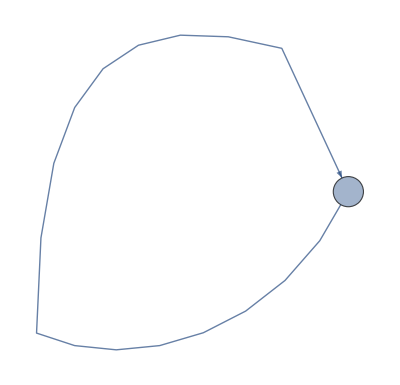
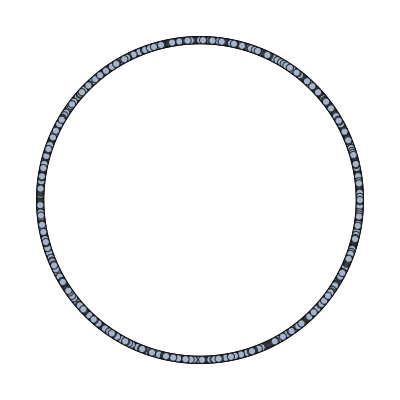
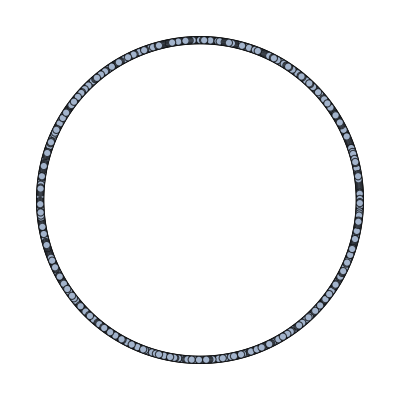
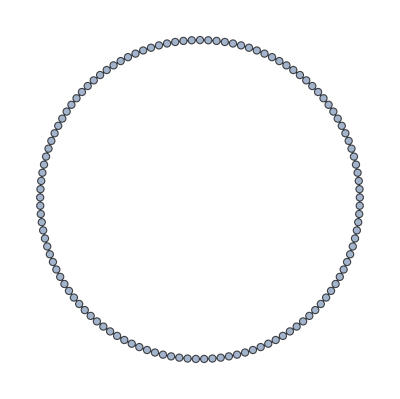
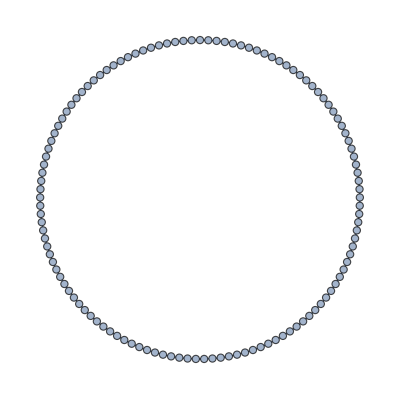
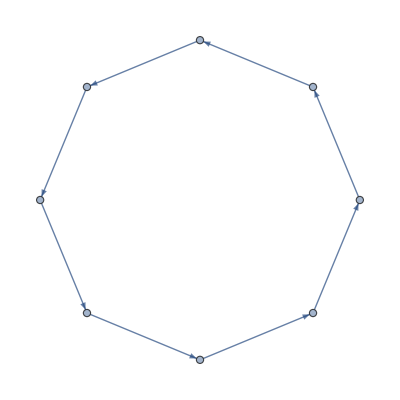

```mathematica
Map[Graph,orbits]
```

```mathematica
TableForm[orbits,TableDepth->3]
```

```mathematica
states
```

```mathematica
MapThread[F,{{a,b,c},{A,B,C}}]
```